```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching "Global`*".

The total mechanical energy of a simple pendulum, with length l and mass m, is given here as TE.  θ is the angle formed by the motion of the pendulum and θt = dθ/dt

```mathematica
$Assumptions={l>0, g> 0, θ > 0, θ < Pi, θn >0, θn < Pi, m > 0};
```

The solve function is used to find dθ

```mathematica
TE = (1/2 )(m l^2 (θt)^2 )+ m g l (1-Cos[θ])==m g l (1-Cos[θn])

sol = Solve[TE,θt] [[2]]
```

1/2 l^2 m θt^2+g l m (1-Cos[θ])==g l m (1-Cos[θn])

{θt→ConditionalExpression[√2 √(g/l) √(Cos[θ]-Cos[θn]), θ<θn]}

Dummy variable is created to transform the expression

```mathematica
b= θt /. sol
```

ConditionalExpression[√2 √(g/l) √(Cos[θ]-Cos[θn]), θ<θn]

Simplify function is used to find the simplest form of the expression

```mathematica
dT = Simplify[(1/b)/ (2Pi Sqrt[l/g])]
```

ConditionalExpression[1/(2 √2 π √(Cos[θ]-Cos[θn])), θ<θn]

Using the integrate function to find the period of oscillation  in relation to dt

```mathematica
T = 4 Integrate[dT,{θ,0,θn}]
```

(2 √2 EllipticF[θn/2,Csc[θn/2]^2])/(π √(1-Cos[θn]))

Plotting the newly integrated function, its shown in the graph that as θn goes to pi, the graph goes to infinity

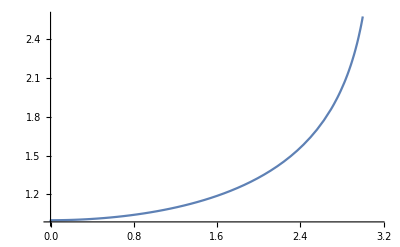

```mathematica
Plot[T,{θn,0,Pi}]
```

Numerical Integration

```mathematica
NIntegrate[T, {θn, 0, Pi}]
```

4.37688

Using the substitute sin(θ/2) = Au to find a new integral for the period as a function of θn

```mathematica
Tθn = 2/Pi Integrate[(1/Sqrt[1-u^2])(1/Sqrt[1-A^2u^2]), {u,0,1}]
```

ConditionalExpression[(2 EllipticK[A^2])/π, Re[A^2]≤1||A^2∉ℝ]

Series function is used to expand to the lowest non zero order

```mathematica
eT = Series[Tθn,{A, 0,2}] /. A  -> Sin[θn/2] // Normal
```

1+1/4 Sin[θn/2]^2

The new function(blue) is plotted on the same graph as the old one(orange) which shows the expansion only works for θn less than one

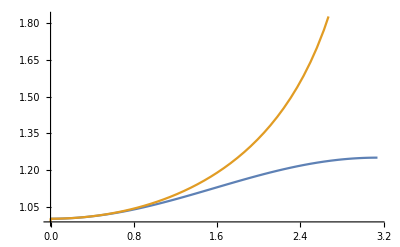

```mathematica
Plot[{eT, T}, {θn, 0, Pi}]
```